```mathematica
Quit
```

## Acknowledgment

### -This Genetic Algorithm code is partially based on : "Suleman, H. (1997). Genetic Programming in Mathematica (Doctoral dissertation)." -If you use this code please cite : “arXiv : 2002.12700, 2001.11420, 1910.01529.” -A different Genetic Algorithm code can be found at: “https://github.com/snesseris/Genetic-Algorithms.”

## Mock data

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
(* Some mock data *)
SeedRandom[12348551];
model[x_,a_,b_,c_]:=a+(x-b) Exp[-c x^2]
σ=0.03;
data=Table[{x,model[x,1/4,1/4,1/2]+RandomVariate[NormalDistribution[0,σ]],RandomVariate[NormalDistribution[σ,σ/5]]},{x,0.025,1.55,0.05}];ndat=Length[data];
```

```mathematica
(* Definitions *)
chi2model[a_,b_,c_]:=Sum[((data[[ii,2]]-model[data[[ii,1]],a,b,c])/data[[ii,3]])^2,{ii,1,Length[data]}];
```

χ^2/dof= 1.02588

Number of points = 31

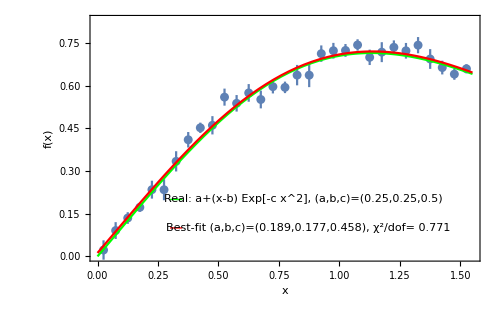

```mathematica
(* Best fit // normal case *)
fmin=FindMinimum[chi2model[a,b,c],{a,0.2},{b,.5},{c,0.5}];
Print["χ^2/dof= ",fmin[[1]]/ndat]
Print["Number of points = ",ndat]
(* Plots of the mock data *)
err=ErrorListPlot[data,PlotRange->{{0,1.55},{0,.83}}];
pl0=Plot[{model[x,1/4,1/4,1/2],model[x,a,b,c]/.fmin[[2]]},{x,0,1.55},PlotStyle->{Green,Red}];
Show[err,pl0,Graphics[{{Green,Line[{{.3,.2},{.35,.2}}]},{Red,Line[{{.3,.1},{.35,.1}}]}}],Frame->True,Axes->False,Epilog->{Text["Real: a+(x-b) Exp[-c x^2], (a,b,c)=(0.25,0.25,0.5)",{.85,.2}],Text["Best-fit (a,b,c)=(0.189,0.177,0.458), χ^2/dof= 0.771",{.87,.1}]},FrameLabel->{"x","f(x)"},ImageSize->500]
```

```mathematica
(* end *)
```

## Genetic Algorithm

```mathematica
(*Extra definitions*)
```

```mathematica
ClearAttributes[Divide,Protected]
Divide[_,0]:=1
SetAttributes[Divide,Protected]
```

```mathematica
ClearAttributes[Log,Protected]
Log[0]:=0
Log[x_/;x<0]:=Log[-x]
Log[E^x_]:=x
SetAttributes[Log,Protected]
```

```mathematica
ClearAttributes[Power,Protected]
Power[0,-1]:=1
SetAttributes[Power,Protected]
```

```mathematica
Grammar={PPlus,PPlus,PPlus,PTimes,PTimes,PMinus};
Parameters={2,2,2,2,2,1} ;(* It tells how many parameters each operation can take *)
```

```mathematica
(* Grammar = PPlus, PTimes, PMinus, PDivide, PExp, PPower, PLog, PSin, PCos, PTan *)
```

```mathematica
SeedRandom[30]
Terminals={-RandomReal[{0.095,3}],RandomReal[{0.06,1.4}]Exp[-RandomReal[{0.07,3.3}]x] x^(RandomReal[{0.009,0.7}]x)};
```

```mathematica
(* Specifications. Play with it *)
```

```mathematica
MaxComplexity=50;
MaxGenerations=1000;
PopulationSize=4000;
CrossoverProbability=0.75;
MutationProbability=0.25;
MaxSize=17;
MaxInitialSize=5;
```

```mathematica
(* χ^2 for GA *)
```

```mathematica
chi2GA[f_]:=Module[{temp,ft},ft=(f/.XTrans/.x->#)&;temp=Sum[((data[[ii,2]]-(data[[ii,1]]+data[[ii,1]]^2(1+ft[data[[ii,1]]])))/data[[ii,3]])^2,{ii,1,Length[data]}]];
RawFitness[expr_]:=Check[chi2GA[expr],200000]/20
```

```mathematica
(* GA Algorithm. Create Population, Crossover, Mutation, Roulette Wheel *)
```

```mathematica
(*Generate random expression*)
```

```mathematica
GenerateNormal[d_]:=Module[{r,Poss,PossPar},If[d>1,Poss=Join[Grammar,Terminals];
PossPar=Parameters,Poss=Terminals;
PossPar={}];
While[Length[PossPar]<Length[Poss],PossPar=Append[PossPar,0]];
r=Random[Integer,{1,Length[Poss]}];
Switch[PossPar[[r]],0,Poss[[r]],1,Poss[[r]][Generate[d-1]],2,Poss[[r]][Generate[d-1],Generate[d-1]],3,Poss[[r]][Generate[d-1],Generate[d-1],Generate[d-1]]]]
```

```mathematica
Generate[d_]:=Module[{y},y=GenerateNormal[d];While[LeafCount[y]>MaxComplexity,y=GenerateNormal[d]];y]
```

```mathematica
(*Get list of all indices of internal points in expression*)
```

```mathematica
RemoveZero[x_]:=If[Position[x,0]=={},x,{}]
Points[x_]:=Union[Map[RemoveZero,Position[x,_]],{}]
GetInternal[{x___}]:=x
```

```mathematica
(*Perform crossover operation on two expressions*)
```

```mathematica
Cross1[x_,y_]:=Module[{spot1,spot2,point1,point2,temp1,temp2},If[Random[]<CrossoverProbability,point1=Points[x];
spot1=Random[Integer,{1,Length[point1]}];
point2=Points[y];
spot2=Random[Integer,{1,Length[point2]}];
temp1=x[[GetInternal[point1[[spot1]]]]];
temp2=y[[GetInternal[point2[[spot2]]]]];
{If[point1[[spot1]]=={},temp2,ReplacePart[x,temp2,point1[[spot1]]]],If[point2[[spot2]]=={},temp1,ReplacePart[y,temp1,point2[[spot2]]]]},{x,y}]]
```

```mathematica
(*Perform mutation operation on an expression*)
```

```mathematica
Mutate[x_]:=Module[{spot1,point1,y,xold},xold=x;
If[Random[]<MutationProbability,y=Generate[MaxInitialSize];
point1=Points[x];
spot1=Random[Integer,{1,Length[point1]}];
If[point1[[spot1]]=={},y,ReplacePart[x,y,point1[[spot1]]]],If[((Depth[x]<MaxSize)&&(LeafCount[x]<MaxComplexity)),x,xold]]]
```

```mathematica
(*RawFitness*)
```

```mathematica
StandardizedFitness[x_]:=RawFitness[x]
```

```mathematica
AdjustedFitness[x_]:=N[1/(1+StandardizedFitness[x])]
```

```mathematica
(*List of fitnesses of expressions in current generation*)
```

```mathematica
Fitnesses={};
```

```mathematica
(*Make cumulative fitnesses vector*)
```

```mathematica
CalcFitnessSum:=Module[{},FitSum=Table[Apply[Plus,Take[Fitnesses,i]],{i,1,Length[Fitnesses]}];
FitSum=Insert[FitSum,0,1];]
```

```mathematica
(*Bisection algorithm search for roulette wheel fitness choice*)
```

```mathematica
Search[x_]:=Module[{Mid,Start=1,Stop=Length[FitSum]},While[Start+1!=Stop,Mid=Floor[(Start+Stop)/2];
If[FitSum[[Mid]]>x,Stop=Mid,Start=Mid]];
Start]
```

```mathematica
(*Create new generation from previous one*)
```

```mathematica
NewGen[x_]:=Module[{maxwheel,newgen,lenx},newgen={};
maxwheel=Apply[Plus,Fitnesses];
lenx=Length[x];
CalcFitnessSum;
Do[Module[{spot,index,isum},spot=Random[]*maxwheel;
index=Search[spot];
newgen=Append[newgen,x[[index]]]],{i,1,lenx}];
newgen]
```

```mathematica
(*Perform crossover on all expressions in new generation*)
```

```mathematica
Crossover[x_]:=Module[{newx,oldx,n2,leno,origlen},oldx=x;
newx={};
leno=Length[oldx];
origlen=leno;
While[leno>0,If[leno==1,newx=Append[newx,First[oldx]];
oldx=Rest[oldx],n2=Cross1[oldx[[1]],oldx[[2]]];
If[((Depth[n2[[1]]]<=MaxSize)&&(LeafCount[n2[[1]]]<=MaxComplexity)),newx=Append[newx,n2[[1]]],newx=Append[newx,oldx[[1]]]];
If[((Depth[n2[[2]]]<=MaxSize)&&(LeafCount[n2[[2]]]<=MaxComplexity)),newx=Append[newx,n2[[2]]],newx=Append[newx,oldx[[2]]]];
oldx=Drop[oldx,2];
];
leno=Length[oldx]
];
newx
]
```

```mathematica
(*Solution,SolutionFitness,SolutionSet*)
```

```mathematica
(*Update best-of-run individual*)
```

```mathematica
CheckSolution[gen_,x_]:=Module[{minf,maxf},Fitnesses=AdjustedFitness/@x;
minf=Position[Fitnesses,Min[Fitnesses]][[1,1]];
maxf=Position[Fitnesses,Max[Fitnesses]][[1,1]];
If[SolutionFitness<Fitnesses[[maxf]],Solution=x[[maxf]];
SolutionFitness=Fitnesses[[maxf]]];
SolutionSet=Append[SolutionSet,{gen,Fitnesses[[maxf]],x[[maxf]],Fitnesses[[minf]],x[[minf]]}];
Print["G",gen,": max ",Fitnesses[[maxf]]," min ",Fitnesses[[minf]]];]
```

```mathematica
MinFitness=0.99;
```

```mathematica
(*Generation,Population,TotTime*)
```

```mathematica
XTrans={PPlus->Plus,PMinus->Minus,PTimes->Times,PDivide->Divide,PPower->Power,PExp->Exp, PLog->Log, PSin->Sin, PCos->Cos, PTan->Tan};
```

```mathematica
(*Apply Genetic algorithm*)
```

```mathematica
MaxInitialSize=5;
```

```mathematica
(*Initialise Genetic algorithm*)
```

```mathematica
Initialize=Block[{poplog},Population=Table[Generate[MaxInitialSize],{PopulationSize}];
SolutionFitness=0;
SolutionSet={};
Generation=0;
TotTime=0;
Print["G",Generation,": calculating fitnesses ..."];
Print["G",Generation,": done ... ",Timing[CheckSolution[Generation,Population]][[1]]];
Print["G",Generation,": best-of-run fitness so far = ",SolutionFitness];
Off[DeleteFile::nffil];
DeleteFile["pop.log"];
DeleteFile["restart.log"];
DeleteFile["restart.new"];
DeleteFile["restart.old"];
On[DeleteFile::nffil];
poplog=OpenAppend["pop.log"];
WriteString[poplog,"pop={"];
Write[poplog,{Generation,Fitnesses}];
Close[poplog];
Save["restart.log",PopulationSize];]
```

G0: calculating fitnesses ...

G0: max 0.392164 min 0.000019349

G0: done ... 7.3125

G0: best-of-run fitness so far = 0.392164

DeleteFile::fdnfnd: Directory or file restart.new not found.

DeleteFile::fdnfnd: Directory or file restart.old not found.

Set::wrsym: Symbol Initialize is Protected.

```mathematica
Initialize;
```

```mathematica
Solution/.XTrans
chi2GA[Solution/.XTrans]
```

-1.52174+1.1373 ⅇ^(-1.66335 x) x^(0.661286 x)+0.656097 ⅇ^(-3.32671 x) x^(1.32257 x)

30.9991

```mathematica
(* end *)
```

## Error Analysis

```mathematica
Quit
```

```mathematica
chi2[f_,dat_]:=Module[{temp,ft},ft=(f/.x->#)&;temp=Sum[((dat[[ii,2]]-(ft[dat[[ii,1]]]))/dat[[ii,3]])^2,{ii,1,Length[dat]}]];
```

```mathematica
(* The GA best-fit *)
```

```mathematica
fGA[x_]:=x+x^2 (1-1.521744066803322+1.1372970485007503 ⅇ^(-1.6633546639883834 x) x^(0.6612855617031306 x)+0.6560972033570691 ⅇ^(-3.3267093279767668 x) x^(1.3225711234062612 x))
```

```mathematica
(* Compare the chi^2 *)
```

```mathematica
chi2[model[x,a,b,c]/.fmin[[2]],data]
chi2[fGA[x],data]
```

31.8024

30.9991

```mathematica
(* Error analysis doing the path integral approach. For details see: arXiv:1205.0364*)
```

```mathematica
df[x_,a1_,a2_,a3_,a4_]:=x(a1+a2 x+a3 x^2+a4 x^3)
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3,a4]+fGA[data[[i,1]]]-data[[i,2]])]+Erf[1/(√2 data[[i,3]])(df[data[[i,1]],a1,a2,a3,a4]-fGA[data[[i,1]]]+data[[i,2]])])/Erf[1/(√2)],{i,1,Length[data]}];
Sum[(CI[[i]]-1)^2,{i,1,Length[data]}]]
chi2GAerr[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=chi2[fGA[x]+df[x,a1,a2,a3,a4],data]
chi2tot[a1_,a2_,a3_,a4_]:=chi2CI[a1,a2,a3,a4]+chi2GAerr[a1,a2,a3,a4]
```

```mathematica
fminerr2=FindMinimum[chi2tot[a1,a2,0,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
fminerr3=FindMinimum[chi2tot[a1,a2,a3,0],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},MaxIterations->500]
fminerr4=FindMinimum[chi2tot[a1,a2,a3,a4],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},{a4,0.11,0.111},MaxIterations->500]
```

{57.7399,{a1→0.0220018,a2→-0.0126533}}

{57.4316,{a1→0.0409232,a2→-0.0514469,a3→0.0179828}}

{55.3062,{a1→0.131109,a2→-0.408175,a3→0.418295,a4→-0.135441}}

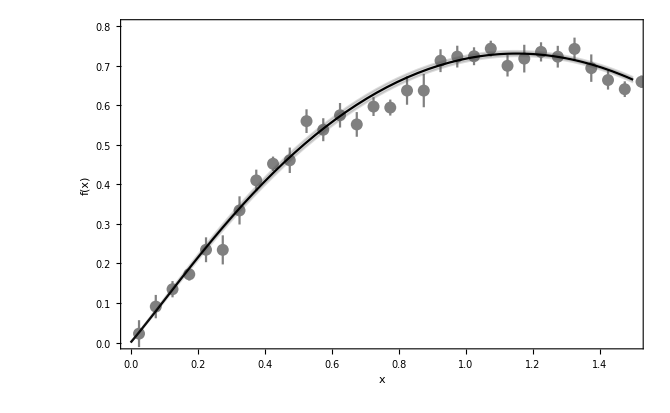

```mathematica
(* Final plot with errors *)
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plr={{0,1.5},{0,.8}};
plot=Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[fGA[x]+ϵ0 df[x,a1,a2,a3,0a4]/.fminerr3[[2]]//Evaluate,{x,0,1.5},PlotRange->plr,Frame->True,PlotStyle->{col,Black,col},Filling->{1->{{3},col}}],Frame->True,Axes->False,FrameLabel->{"x","f(x)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr]
```

```mathematica
Export["GA_fit.pdf",plot,ImageSize->500]
```

```mathematica
(* end *)
```